```mathematica
SetDirectory[NotebookDirectory[]];
framePoints=Import["LiveTrackedLines (nr,x,y).csv"];
```

## PenTracking - Genauigkeit überprüfen

Die Webcam liefert eine Auflösung von 640x480 ca. alle 40ms. Der PenTracker sucht auf jedem dieser Bilder nach dem Stift. Im folgenden werden alle gefundenen Punkte analysiert.
Es wurde gezeichnet:
- ein paar waagrechte Linien (Massstab)
- eine senkrechte Linie (mit Massstab)
- der Buchstabe “e”
- der Buchstabe “x”

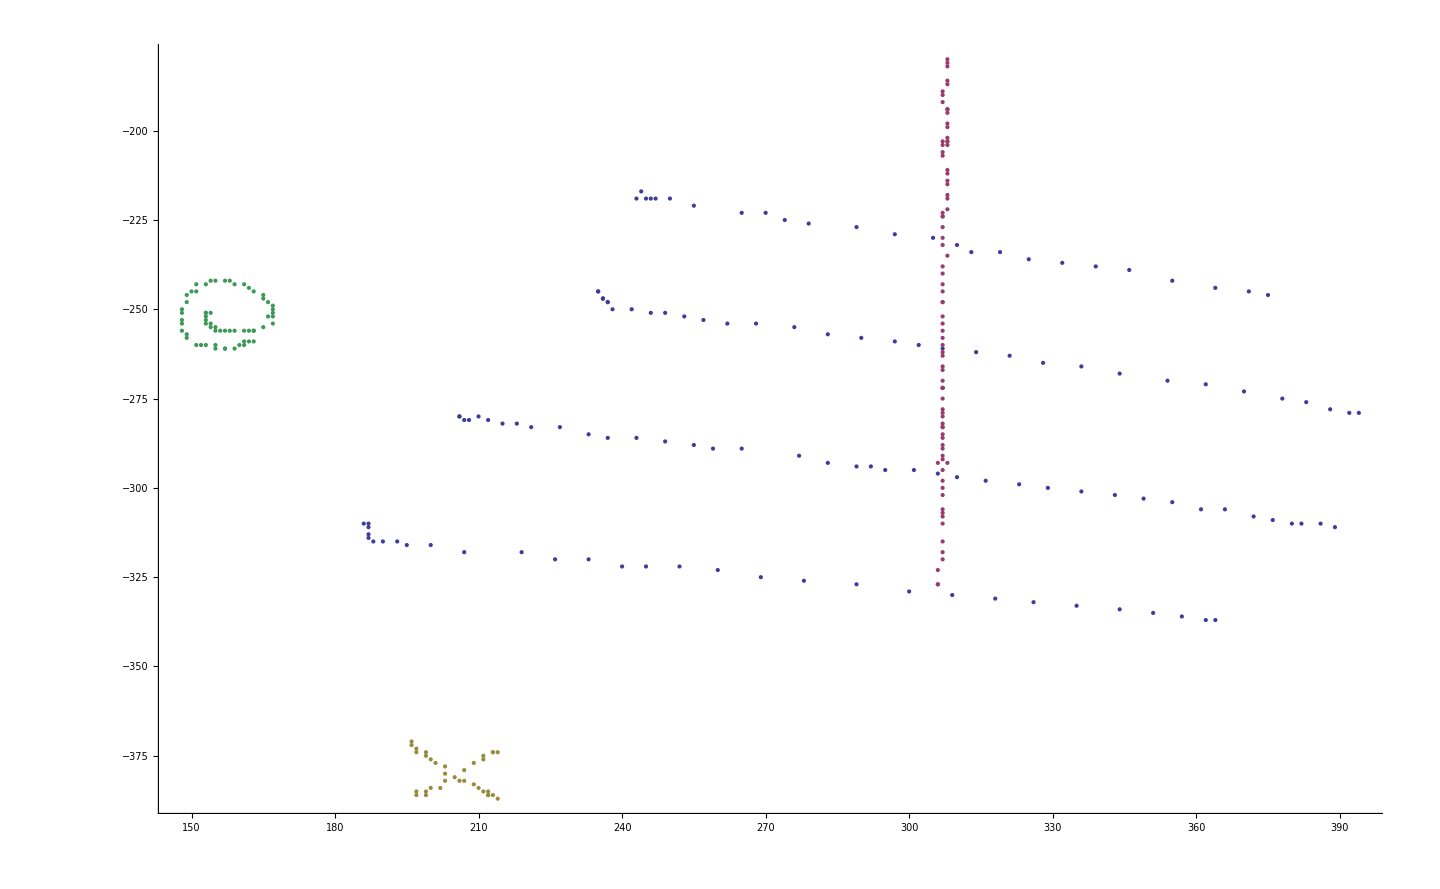

```mathematica
drawablePoints=Table[{framePoints[[n,2]],-framePoints[[n,3]]},{n,Length[framePoints]}];
evenLineRange={533,662};
unevenLineRange={450,532};
xLetterRange= {1065,1099};
eLetterRange={960,1021};
ListPlot[{
Take[drawablePoints,evenLineRange],
Take[drawablePoints,unevenLineRange],
Take[drawablePoints,xLetterRange],
Take[drawablePoints,eLetterRange]
},PlotRange->{{0,640},{0,-480}}]
```

### Analyse der waagrechten Linien

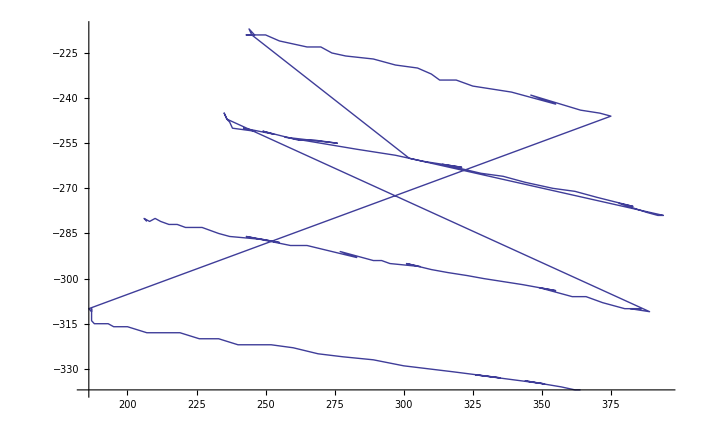

```mathematica
ListLinePlot[Take[drawablePoints,evenLineRange]]
```

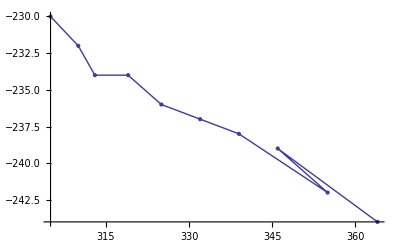

Nr | X | Y
7599 | 305 | 230
7600 | 310 | 232
7602 | 313 | 234
7604 | 319 | 234
7606 | 325 | 236
7608 | 332 | 237
7610 | 339 | 238
7615 | 355 | 242
7612 | 346 | 239
7617 | 364 | 244

```mathematica
failedLineRange=evenLineRange+{87,-33};
Show[ListLinePlot[Take[drawablePoints,failedLineRange]],ListPlot[failedLine]]
TableForm[
With[{marked=7612},#/.marked->Style[marked,Red]]&/@Take[framePoints,failedLineRange],
TableHeadings->{None,{"Nr","X","Y"}}]
```

Der Punkt 7615 hat die 7612 überholt!

### Analyse der senkrechten Linie

Die waagrechte Linie kam erstaunlich gut daher. Es besteht maximal ein Pixel Abstand von der gezeichneten Linie.

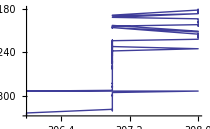

```mathematica
Show[ListLinePlot[unevenLinePoints]]
```

### Analyse des Buchstaben “e”

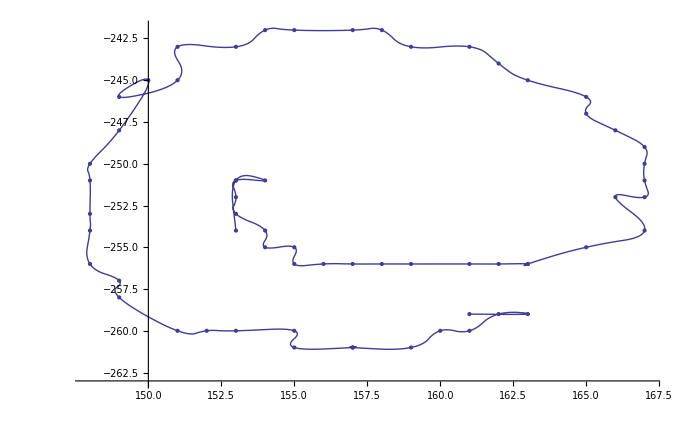

```mathematica
Show[
ListLinePlot[Take[drawablePoints,eLetterRange],InterpolationOrder->2],ListPlot[Take[drawablePoints,eLetterRange]]
]
```

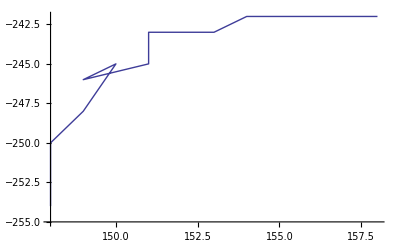

Nr | X | Y
21579 | 158 | 242
21580 | 157 | 242
21581 | 155 | 242
21582 | 154 | 242
21583 | 153 | 243
21584 | 151 | 243
21585 | 151 | 245
21586 | 149 | 246
21587 | 150 | 245
21588 | 149 | 248
21589 | 148 | 250
21590 | 148 | 251
21591 | 148 | 253
21592 | 148 | 254

```mathematica
failedELetterRange=eLetterRange+{32,-16};
Show[ListLinePlot[Take[drawablePoints,failedELetterRange],InterpolationOrder->1],ListPlot[failedELetterRange]]
TableForm[
With[{marked=21586},#/.marked->Style[marked,Green]]&/@Take[framePoints,failedELetterRange],
TableHeadings->{None,{"Nr","X","Y"}}]
```

Mit diesem Resultat ist alles in Ordnung. Wahrscheinlich wurde das Zentrum des Stiftes vom PenTracker nicht richtig gefunden.

### Analyse des Buchstaben “x”

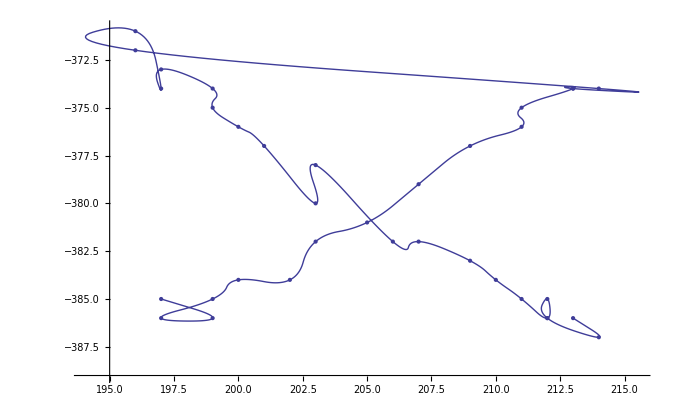

```mathematica
Show[
ListLinePlot[Take[drawablePoints,xLetterRange],InterpolationOrder->2],ListPlot[Take[drawablePoints,xLetterRange]]
]
```

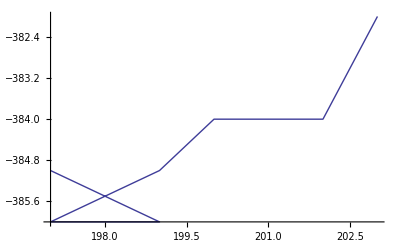

Nr | X | Y
22091 | 197 | 385
22094 | 199 | 386
22092 | 197 | 386
22095 | 199 | 385
22096 | 200 | 384
22098 | 202 | 384
22099 | 203 | 382

```mathematica
failedXLetterRange=xLetterRange+{0,-28};
Show[ListLinePlot[Take[drawablePoints,failedXLetterRange]],ListPlot[failedXLetterRange]]
TableForm[
With[{marked=22092},#/.marked->Style[marked,Red]]&/@Take[framePoints,failedXLetterRange],
TableHeadings->{None,{"Nr","X","Y"}}]
```

Auch hier wurde wieder ein Frame überholt.

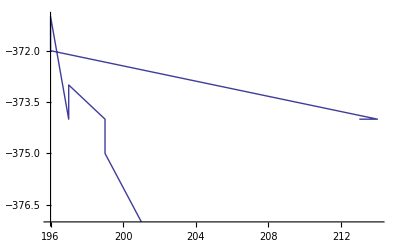

Nr | X | Y
22108 | 213 | 374
22110 | 213 | 374
22111 | 214 | 374
22136 | 196 | 372
22137 | 196 | 371
22139 | 197 | 374
22138 | 197 | 373
22140 | 199 | 374
22141 | 199 | 375
22142 | 200 | 376
22143 | 201 | 377

```mathematica
failedXLetterRange=xLetterRange+{12,-12};
Show[ListLinePlot[Take[drawablePoints,failedXLetterRange]],ListPlot[failedXLetterRange]]
TableForm[
With[{marked=22138},#/.marked->Style[marked,Red]]&/@Take[framePoints,failedXLetterRange],
TableHeadings->{None,{"Nr","X","Y"}}]
```

Auch hier: 22138 wurde überholt.

### Zähle, wieviele male ein Frame überholt wurde

```mathematica
frameNumbers=Map[Take[#,1][[1]]&,framePoints];
overtakes=0;
For[i=2,i<Length[frameNumbers],i++,
overtakes+=If[frameNumbers[[i-1]]<frameNumbers[[i]],"ok",1"überholt"];
]
overtakes
```

1657 ok+139 überholt

Es werden also ca. 10% aller Frame in falscher Reihenfolge erfasst.